# octet.experiment.rencon1.figure.lambda-merge.style-3.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.paper.chpt.ed10\octet.experiment.rencon1.figure.lambda-merge.style-3.nb

this nb is to record the octet ge gm experiment data.

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
fig`calc`nucleon`ge`u = {0, 0, 0};
fig`calc`nucleon`ge`d = {0, 0, 0};
fig`calc`nucleon`ge`s = {0, 0, 0};
```

```mathematica
fig`calc`nucleon`gm`u = {0, 0, 0};
fig`calc`nucleon`gm`d = {0, 0, 0};
fig`calc`nucleon`gm`s = {0, 0, 0};
```

```mathematica
style`exp={
AbsoluteThickness[_]-> AbsoluteThickness[0.5],
PointSize[_]->PointSize[0.02]
};
```

```mathematica
style`calc={
AbsoluteThickness[_]-> AbsoluteThickness[0.5]
};
```

```mathematica
directory`fig="C:\\Users\\Tom\\Desktop\\octet.fig";
```

## nucleon`ge`light-sea

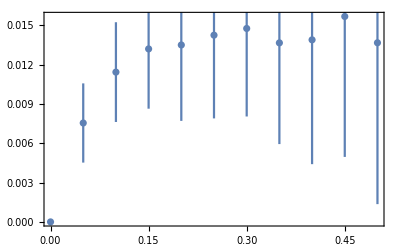
```mathematica
fig`exp`nucleon`ge`lightsea=
-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Blue;
```

## fig`calc`nucleon`ge`u

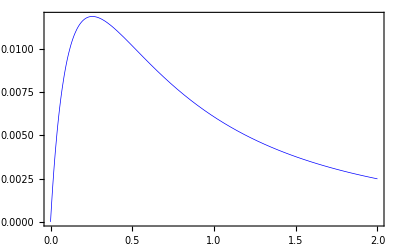

```mathematica
fig`calc`nucleon`ge`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

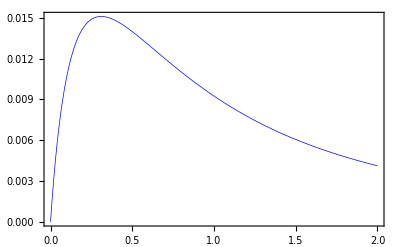

```mathematica
fig`calc`nucleon`ge`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

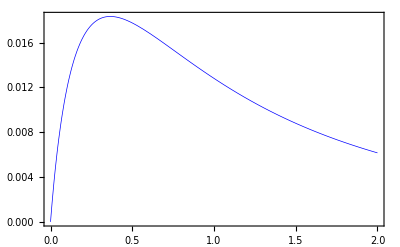

```mathematica
fig`calc`nucleon`ge`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

## fig`calc`nucleon`ge`d

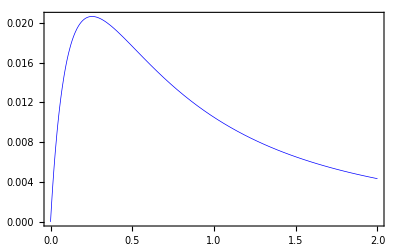

```mathematica
fig`calc`nucleon`ge`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

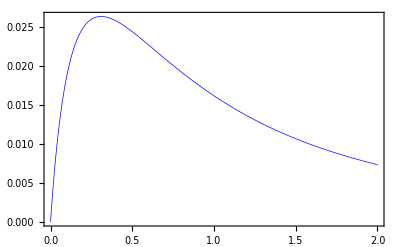

```mathematica
fig`calc`nucleon`ge`d⟦2⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue)
```

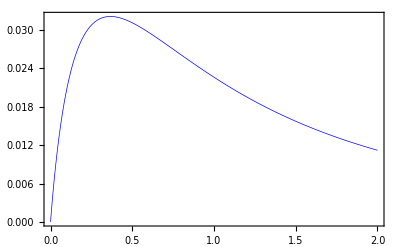

```mathematica
fig`calc`nucleon`ge`d⟦3⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue)
```

## fig`comparison`ge`u

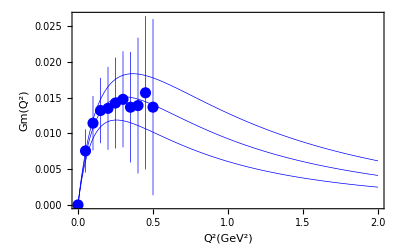

```mathematica
fig`comparison`ge`u=Show[
{fig`exp`nucleon`ge`lightsea,fig`calc`nucleon`ge`u⟦1⟧,fig`calc`nucleon`ge`u⟦2⟧,fig`calc`nucleon`ge`u⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`ge`d

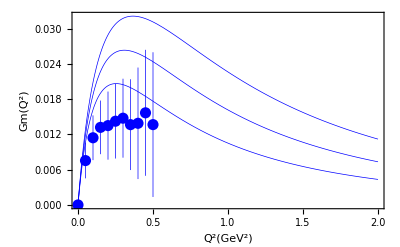

```mathematica
fig`comparison`ge`d=Show[
{fig`exp`nucleon`ge`lightsea,fig`calc`nucleon`ge`d⟦1⟧,fig`calc`nucleon`ge`d⟦2⟧,fig`calc`nucleon`ge`d⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## nucleon`ge`strange

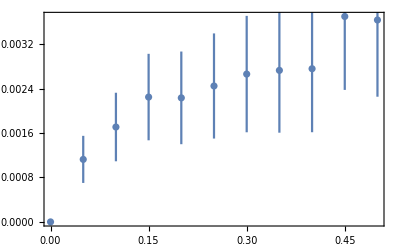
```mathematica
fig`exp`nucleon`ge`s=
-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Red;
```

## fig`calc`nucleon`ge`s

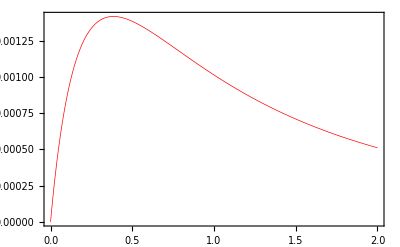

```mathematica
fig`calc`nucleon`ge`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

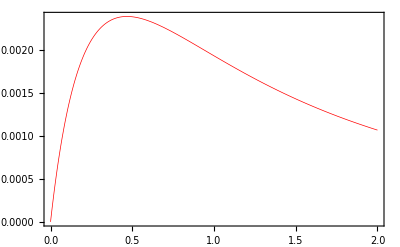

```mathematica
fig`calc`nucleon`ge`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

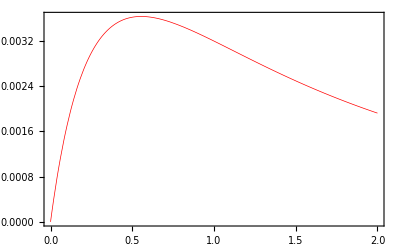

```mathematica
fig`calc`nucleon`ge`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

## fig`comparison`ge`s

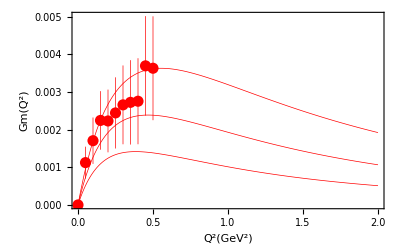

```mathematica
fig`comparison`ge`s=Show[
{fig`exp`nucleon`ge`s,fig`calc`nucleon`ge`s⟦1⟧,fig`calc`nucleon`ge`s⟦2⟧,fig`calc`nucleon`ge`s⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## nucleon`gm`lightsea

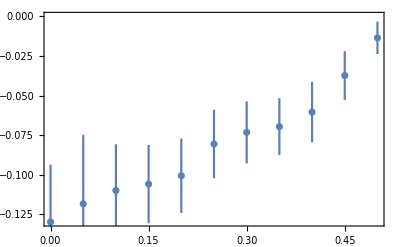
```mathematica
fig`exp`nucleon`gm`lightsea=
-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Blue;
```

## fig`calc`nucleon`gm`u

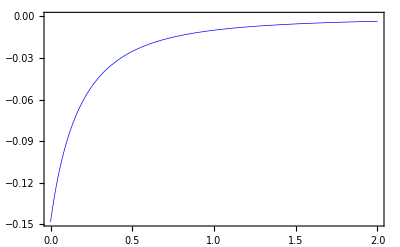

```mathematica
fig`calc`nucleon`gm`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

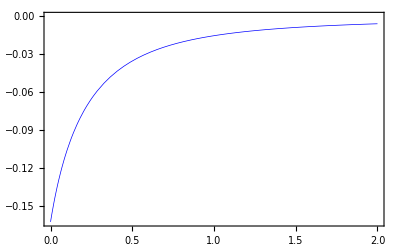

```mathematica
fig`calc`nucleon`gm`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

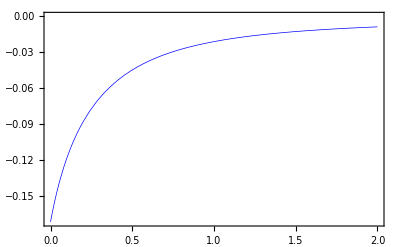

```mathematica
fig`calc`nucleon`gm`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

## fig`calc`nucleon`gm`d

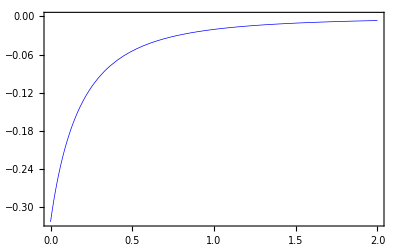

```mathematica
fig`calc`nucleon`gm`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

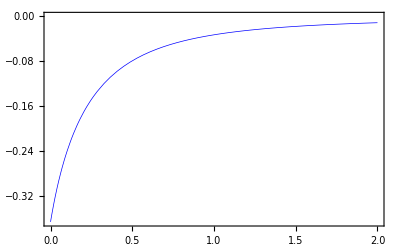

```mathematica
fig`calc`nucleon`gm`d⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

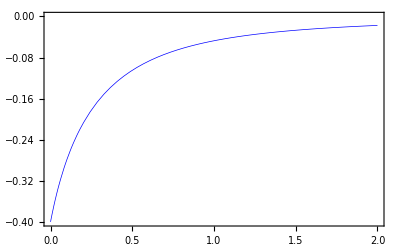

```mathematica
fig`calc`nucleon`gm`d⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

## fig`comparison`gm`u

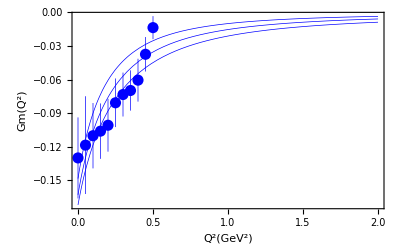

```mathematica
fig`comparison`gm`u=Show[
{fig`exp`nucleon`gm`lightsea,fig`calc`nucleon`gm`u⟦1⟧,fig`calc`nucleon`gm`u⟦2⟧,fig`calc`nucleon`gm`u⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`gm`d

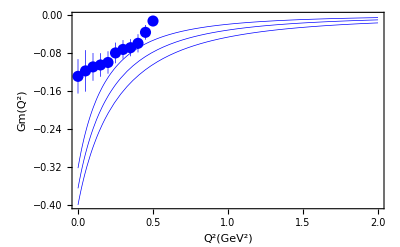

```mathematica
fig`comparison`gm`d=Show[
{fig`exp`nucleon`gm`lightsea,fig`calc`nucleon`gm`d⟦1⟧,fig`calc`nucleon`gm`d⟦2⟧,fig`calc`nucleon`gm`d⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## nucleon`gm`strange

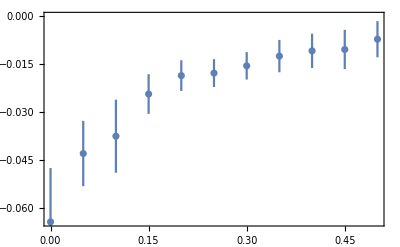
```mathematica
fig`exp`nucleon`gm`s=-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Red;
```

## fig`calc`nucleon`gm`s

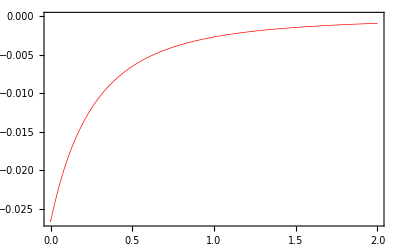

```mathematica
fig`calc`nucleon`gm`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

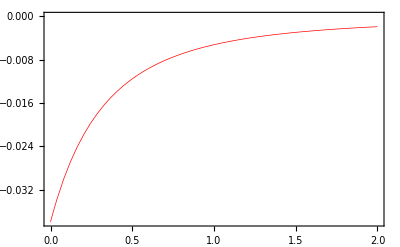

```mathematica
fig`calc`nucleon`gm`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

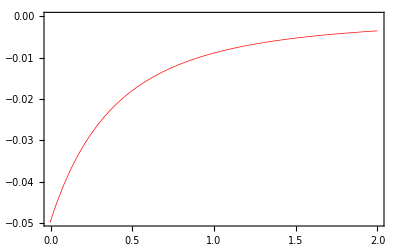

```mathematica
fig`calc`nucleon`gm`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

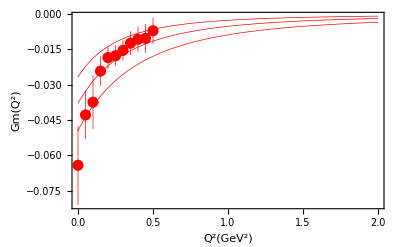

```mathematica
fig`comparison`gm`s=Show[
{fig`exp`nucleon`gm`s,fig`calc`nucleon`gm`s⟦1⟧,fig`calc`nucleon`gm`s⟦2⟧,fig`calc`nucleon`gm`s⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## paper`show

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

u

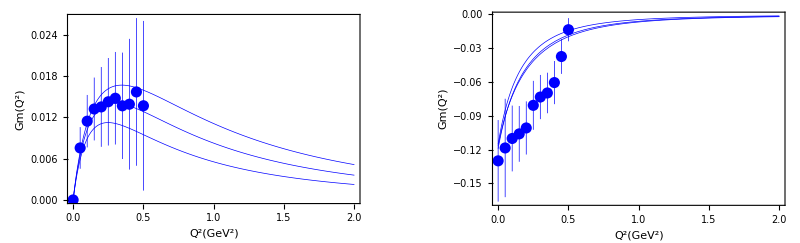
-Graphics-sea u

```mathematica
fig`sea`u=Labeled[
GraphicsGrid[
{{fig`comparison`ge`u(*/.(ImagePadding->_)->(ImagePadding->All)*)(*fig`comparison`ge`u*),fig`comparison`gm`u}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->Automatic,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"sea u"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

d

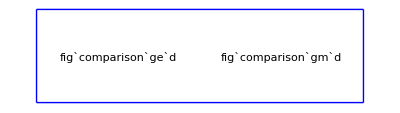
-Graphics-sea d

```mathematica
fig`sea`d=Labeled[
GraphicsGrid[
{{fig`comparison`ge`d/.(ImagePadding->_)->(ImagePadding->All)(*fig`comparison`ge`u*),fig`comparison`gm`d}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"sea d"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]/.{AbsoluteThickness[_]-> AbsoluteThickness[0.5],PointSize[_]->PointSize[0.02]}
```

s

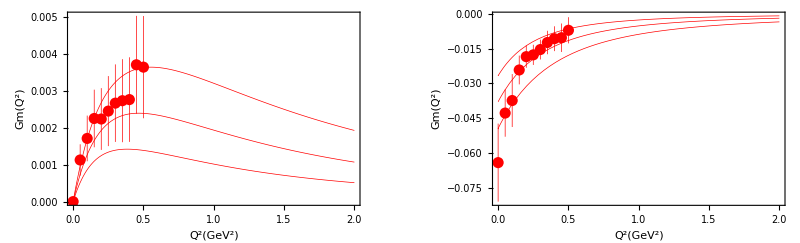
-Graphics-sea s

```mathematica
fig`sea`s=Labeled[
GraphicsGrid[
{{fig`comparison`ge`s,fig`comparison`gm`s}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->Automatic,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"sea s"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

## sea u and s

ge u and s

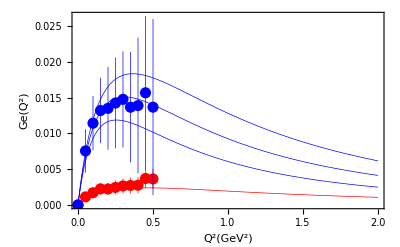
-Graphics-Ge of light-sea and strange

```mathematica
fig`labled`comparison`ge`us=Labeled[
fig`comparison`ge`us=Show[
{
fig`exp`nucleon`ge`s,fig`calc`nucleon`ge`s⟦2⟧,
fig`exp`nucleon`ge`lightsea,fig`calc`nucleon`ge`u⟦1⟧,fig`calc`nucleon`ge`u⟦2⟧,fig`calc`nucleon`ge`u⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Ge of light-sea and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

ge d and s

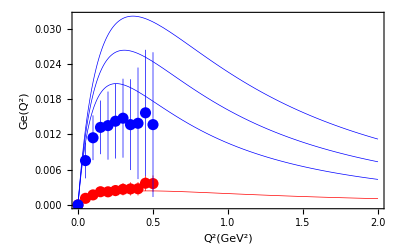
-Graphics-Ge of light-sea and strange

```mathematica
fig`comparison`ge`ds=Labeled[
Show[
{
fig`exp`nucleon`ge`s,fig`calc`nucleon`ge`s⟦2⟧,
fig`exp`nucleon`ge`lightsea,fig`calc`nucleon`ge`d⟦1⟧,fig`calc`nucleon`ge`d⟦2⟧,fig`calc`nucleon`ge`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Ge of light-sea and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

gm u and s

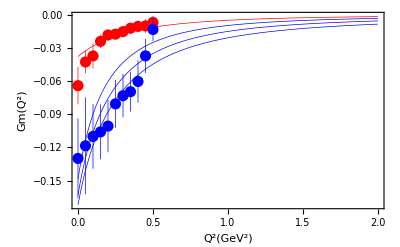
-Graphics-Gm of light-sea and strange

```mathematica
fig`labled`comparison`gm`us=Labeled[
fig`comparison`gm`us=Show[
{
fig`exp`nucleon`gm`s,fig`calc`nucleon`gm`s⟦2⟧,
fig`exp`nucleon`gm`lightsea,fig`calc`nucleon`gm`u⟦1⟧,fig`calc`nucleon`gm`u⟦2⟧,fig`calc`nucleon`gm`u⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Gm of light-sea and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

gm d and s

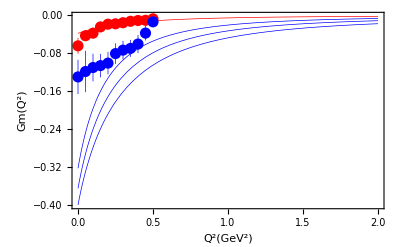
-Graphics-Gm of light-sea and strange

```mathematica
fig`comparison`gm`ds=Labeled[
Show[
{
fig`exp`nucleon`gm`s,fig`calc`nucleon`gm`s⟦2⟧,
fig`exp`nucleon`gm`lightsea,fig`calc`nucleon`gm`d⟦1⟧,fig`calc`nucleon`gm`d⟦2⟧,fig`calc`nucleon`gm`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Gm of light-sea and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

fig`sea`us

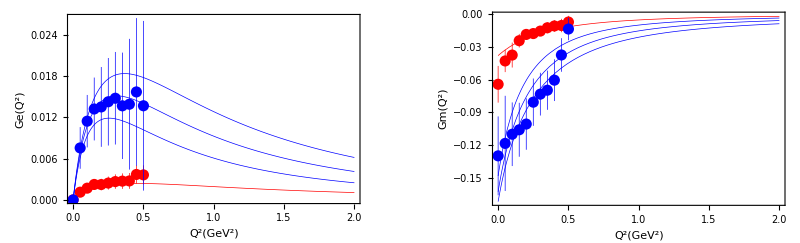
-Graphics-Ge (left side) and Gm (right side)

```mathematica
fig`sea`us=Labeled[
GraphicsGrid[
{{fig`comparison`ge`us,fig`comparison`gm`us}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->Automatic,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"Ge (left side) and Gm (right side)"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

gm u & d

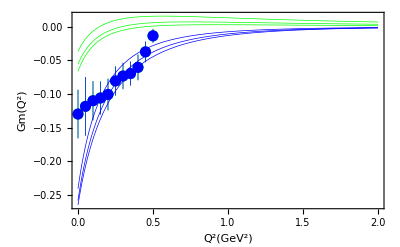

```mathematica
Show[
{fig`comparison`gm`u/.Blue->Green,fig`comparison`gm`d},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

export

```mathematica
SetDirectory["C:\\Users\\Tom\\Desktop\\octet.paper.ed7"];
```

```mathematica
Export["fig3.eps",fig`labled`comparison`ge`us];
```

```mathematica
Export["fig4.eps",fig`labled`comparison`gm`us];
```